Computes expectation of 1/x and 1/x^2 for a truncated normal distribution.

```mathematica
l = 1/2; u = 3+1/2; μ= 2; σ = 1/4;
```

```mathematica
𝒟 = TruncatedDistribution[{l,u},NormalDistribution[μ,  σ]]
```

TruncatedDistribution[{1/2,7/2},NormalDistribution[2,1/4]]

```mathematica
NIntegrate[1/x  PDF[𝒟, x], {x, l, u}]
```

0.508211

```mathematica
NumberForm[%,16]
```

0.5082109850109712

```mathematica
NIntegrate[1/(x x ) PDF[𝒟, x], {x, l, u}]
```

0.262752

```mathematica
NumberForm[%,16]
```

0.2627515620144445

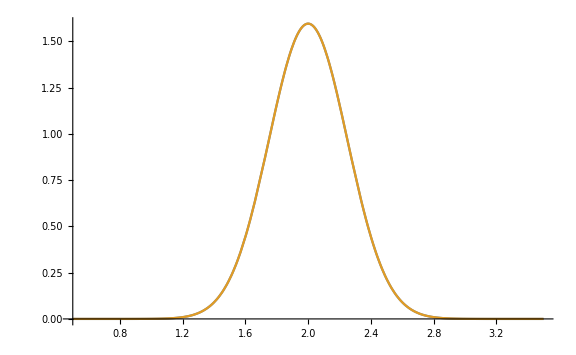

```mathematica
Plot[{PDF[𝒟, x], PDF[NormalDistribution[μ, σ],x]}, {x, l, u}, ImageSize->Large]
```